# Quantica

## Calculator of quantum systems with mathematica

20 December, 2013

## Baker-Campbell-Hausdorff展開

Baker-Campbell-Hausdorff展開の公式は互いに非可換なx,yに対して

e^x e^y=e^z,          z= x+ y + ∑_(j=2)^∞ z_j

と展開される．ここでz_jはxとyの交換間関係が入れ子になった級数として求まる．
各j番目のz_jをmathematicaを用いて交換関係を展開した形式で求める．
なおj>2でなければならない．

```mathematica
Get["Quantica`"];
BCH`Translated2[2]
```

xy/2-yx/2

```mathematica
BCH`Translated2[3]
```

xxy/12-xyx/6+xyy/12+yxx/12-yxy/6+yyx/12

同様に3項のBCH展開

e^x e^y e^w=e^z,           z= x+ y + w + ∑_(j=2)^∞ z_j

は

```mathematica
BCH`Translated3[2]
```

-wx/2-wy/2+xw/2+xy/2+yw/2-yx/2

としてとともめる事が可能である．
さらに対称性がある場合

e^x e^y e^x=e^z,           z= 2x+ y + ∑_(j=2)^∞ z_j

は

```mathematica
BCH`Translated3S[2]
BCH`Translated3S[3]
BCH`Translated3S[4]
```

0

-xxy/6+xyx/3+xyy/6-yxx/6-yxy/3+yyx/6

0

となる．対称な場合z_j の偶数次はゼロとなる

## 量子写像のBCH展開近似

量子写像にBCH公式を適用し

exp[-ⅈ/ℏT(p)τ]exp[-ⅈ/ℏV(p)τ]≃exp[-ⅈ/ℏ H_eff^(m)τ]

H_eff^(m)(q,p)= T(p) + V(q) + ∑_(j=2)^m s^(j-1)H_j(q,p), where s =(-ⅈ/ℏτ)

Summationをm次までで打ち切る事で近似的に求まる時間に依存しないハミルトニアンを求める．

```mathematica
Exit[]
```

```mathematica
Get["Quantica`"];
Quantica`MP`dps=20;
T[x_]:=x*x/2
V[x_]:=Cos[2*Pi*x]/(4*Pi*Pi)
dim=70;
domain={{0,1},{-1,1}};
QuanticaSetting[dim,domain,tau->6/10];
SetSystem[T,V];
matT=FourierBase`MatrixT[];
matV=FourierBase`MatrixV[];
Ham=FourierBase`Hamiltonian[];
A=-I*matT*Tau/Hbar;
B=-I*matV*Tau/Hbar;
evals = {};
```

{Dim:,70,Domain:,{{0,1},{-1,1}},Tau:,3/5,dps:,20}

```mathematica
For[i=1,i<5,i++,
Print[i];
res = BCH`BCH2[i,A,B,Verbose->False,KernelNum->2];
mat= Hbar*I*res/Tau;
evals=Append[evals,Eigen[mat,Vector->False]];
];
```

1

2

3

4

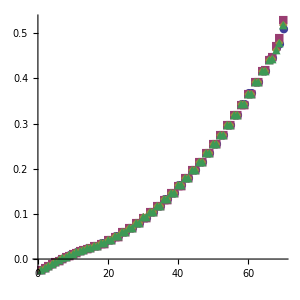

```mathematica
ListPlot[Table[  Re[evals[[i]]  ],{i,1,Length[evals]} ],
PlotMarkers->{Automatic,Small},ImageSize->{300,300},AspectRatio->Full]
```

3項の場合は

```mathematica
For[i=1,i<6,i+=2,
res = BCH`BCH3[i,B/2,A,B/2,Verbose->True,KernelNum->2];
mat= Hbar*I*res/Tau;
evals=Append[evals,Eigen[mat,Vector->False]];
];
```

{2 word Symmetric BCH series:,3}

{2 word Symmetric BCH series:,3}

{2 word Symmetric BCH series:,5}

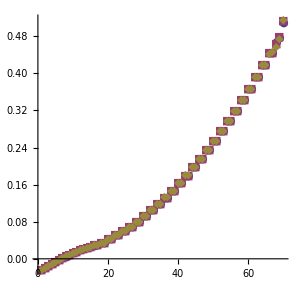

```mathematica
ListPlot[Table[  Re[evals[[i]]  ],{i,1,Length[evals]} ],
PlotMarkers->{Automatic,Small},ImageSize->{300,300},AspectRatio->Full]
```

とすればよい．

## BCHハミルトニアン作用素

BCH展開を用いる事で，ハミルトン行列を作る事ができる事を前節で確認した．
本節では演算子表現を与えるサンプルプログラムを示す．
まず，時間発展のBCH近似ハミルトニアンH_eff^(m)考える．

e^(sT(p))e^(sV(q))=e^(sH(q,p)), where s = -ⅈ/ℏτ

H_eff^(m)(q,p)=  ∑_(j=1)^m s^(j-1) H_j(q,p)

ここで各H_jを交換子を用いて明示的に書くと

H_1(q,p) = T(p) + V(q),
H_1(q,p)=1/2[T,V],
H_2(q,p) = 1/12{[T,[T,V]] -[V,[T,V]}
⋮

である．簡単の為

T(p)=p^2/2

として．正準量子化

p→ℏ/ⅈ ⅆ/ⅆq

と置き換えることにより，BCHの第一項H_1は典型的なSchrödinger 方程式

H_1(q,p) ψ(q) = (-ℏ^2/2ⅆ^2/(ⅆ q^2) + V(q))ψ(q)

を提供する．ではBCHの展開項H_jから導かれる波動関数ψ(q)の微分方程式を導出しよう．簡単な計算により

H_2(q,p)ψ(q) = (-ℏ^2/4)(2V'(q)ⅆ/ⅆq +V''(q))ψ(q)

である事が分かる．Quanticaを用いてこれを確かめるには

```mathematica
Exit[]
```

```mathematica
Get["Quantica`"];
T[x_]:=x^2/2;
```

```mathematica
{res, replace} = BCH`BCH2Operation[2,T,V] ;
res
```

-1/2 S ℏ^2 V'[q] ψ'[q]-1/4 S ℏ^2 ψ[q] V''[q]

BCH2Operationの計算では計算では係数Sが掛かっているが
，BCH2OperationがBCH展開のs^(j-1)H_jを計算しているからである．故にSで割れば

```mathematica
res/S//Expand
```

-1/2 ℏ^2 V'[q] ψ'[q]-1/4 ℏ^2 ψ[q] V''[q]

式(12)が正しく求まっている事が分かるであろう．ここから，ハミルトニアンをqとpのみを使って書き直すには(10)式の量子化則を逆に

ⅆ/ⅆq→ⅈ/ℏ p

行えば良い．すなわち(12)式は

H_2(q,p)ψ(q) = (-ⅈℏ/2V'(q) p - ℏ^2/4 V''(q))ψ(q)

となるこの操作もBCH2Operationによって既に求まっており，

```mathematica
replace
```

{ψ[q]→1,ψ'[q]→(ⅈ p)/ℏ,ψ''[q]→-p^2/ℏ^2,ψ^(3)[q]→-(ⅈ p^3)/ℏ^3,ψ^(4)[q]→p^4/ℏ^4}

を使って

```mathematica
res/S/.replace //Expand
```

-1/2 ⅈ p ℏ V'[q]-1/4 ℏ^2 V''[q]

と求める事ができる．また全く同じ操作であるが

```mathematica
H2 = BCH`BCH2HamiltonianTerm[2,T,V]
```

-1/2 ⅈ p S ℏ V'[q]-1/4 S ℏ^2 V''[q]

を使う事もできる．さて，(13)式の置き換えにより，ℏの次数が下がっている事が分かるであろう．BCH展開は各H_jにs^(j-1)が掛かっているので

s = -ⅈ/ℏτ

で有る事を思い出せば，

sH_1(q,p)=(-τ/2V'(q) p + ⅈ τℏ/4 V''(q))

となる．

```mathematica
H2/.S->(-I*τ/ℏ) //Expand
```

-1/2 p τ V'[q]+1/4 ⅈ τ ℏ V''[q]

すなわち，すなわち第二項までの展開(m=2)のハミルトニアンは

H_eff^(2)=1/2 p^2 + V(p) -τ/2 V'(q) p + ⅈ τℏ/4 V''(q)

となる．このHamiltonの計算は

```mathematica
Ham= BCH`BCH2Hamiltonian[2,T,V]
```

p^2/2+V[q]-1/2 p τ V'[q]+1/4 ⅈ τ ℏ V''[q]

で提供されている．H_eff^(2)はℏ→0 の極限で残るハミルトニアンを提供する事に気づくであろう1．すなわち，

```mathematica
Coefficient[Ham, ℏ, 0]
```

p^2/2+V[q]-1/2 p τ V'[q]

はBCH展開によってもたらされる古典ハミルトニアンである．全く同じ操作であるが古典ハミルトニアンは

```mathematica
BCH`ClassicalTerm[Ham]
```

p^2/2+V[q]-1/2 p τ V'[q]

で提供されている．Vを定義してHの等エネルギー面を書いてみよう．

```mathematica
V[x_]:=Cos[x];
τ=1;
H[q_,p_]=BCH`ClassicalTerm[Ham]
```

p^2/2+Cos[q]+1/2 p Sin[q]

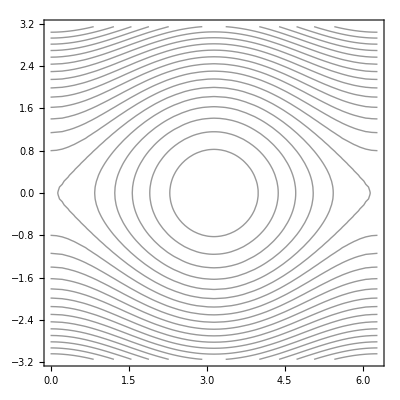

```mathematica
ContourPlot[T[p]+V[q],{q,0,2*Pi},{p,-Pi,Pi},Contours->20,ContourShading->None]
```

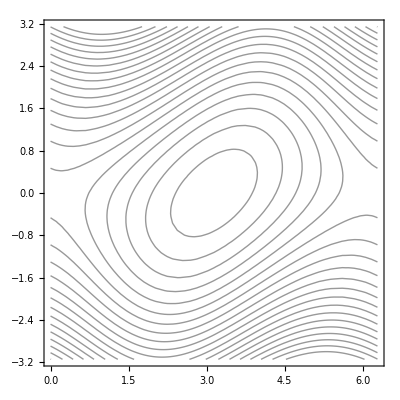

```mathematica
ContourPlot[H[q,p],{q,0,2*Pi},{p,-Pi,Pi},Contours->20,ContourShading->None]
```

標準写像の位相空間構造の様に，変形した等エネルギー面が得られる．

## Reference

1	A. Shudo, Y. Hanada, A. Okushima and K. S. Ikeda submitted peper , see also unpublished note (private network only)